# Microwave Pulses

## Gabriel Patenotte Ni Lab

### Versions

v05042023: Made this notebook based off of my singleQubitPulses.nb notebook.

### Setup

Choosing default plot options, turning off warnings, and picking a color scheme.

```mathematica
SetDirectory["/Users/gabrielpatenotte/Documents/Research/Ni Group/Mathematica"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImageSize->500,AxesLabel->{"",""}]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
```

### Pulses

A wait time is defined as {“w”,τ}, where τ is the wait time.
A pulse is defined as {“p”,θ, v}, where θ is the angle of rotation, and v is the axis of rotation. The Rabi frequency Ω and detuning Δ are assumed to be the same for all pulses, and defined elsewhere.

#### Axes

```mathematica
axes=Association["x"->{1,0,0},"-x"->{-1,0,0},"y"->{0,1,0},"-y"->{0,-1,0},"z"->{0,0,1},"-z"->{0,0,-1}];
```

```mathematica
n[θ_,ϕ_]=Flatten[RotationMatrix[ϕ,"z"/.axes].RotationMatrix[θ,"y"/.axes].({{0}, {0}, {1}})];
```

#### Pulses

Pulse names start with lowercase p. Eta (η) is the pulse time error. Assuming all pulses have the same Rabi frequency.

```mathematica
pPhaseRamsey={{"p",π/2 η,"x"},{"w",τ},{"p",π/2 η,n[π/2,ϕ]}};
pRamsey={{"p",π/2 η,"y"},{"w",τ},{"p",π/2 η,"-y"}};
pPhaseSpinEchoY={{"p",π/2 η,"y"},{"w",τ},{"p",π η,"y"},{"w",τ},{"p",π/2 η,n[π/2,ϕ]}};
pPhaseSpinEchoX={{"p",π/2 η,"y"},{"w",τ},{"p",π η,"x"},{"w",τ},{"p",π/2 η,n[π/2,ϕ]}};
pSpinEchoY={{"p",π/2 η,"y"},{"w",τ},{"p",π η,"y"},{"w",τ},{"p",π/2 η,"-y"}};
pSpinEchoX={{"p",π/2 η,"y"},{"w",τ},{"p",π η,"x"},{"w",τ},{"p",π/2 η,"-y"}};
pXY8X={{"p",π/2 η,"x"},{"w",τ},{"p",π η,"x"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"x"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"x"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"x"},{"w",τ},{"p",π/2 η,"-x"}};
pPhaseXY8X=pXY8X={{"p",π/2 η,"x"},{"w",τ},{"p",π η,"x"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"x"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"x"},{"w",2τ},{"p",π η,"y"},{"w",2τ},{"p",π η,"x"},{"w",τ},{"p",π/2 η,n[π/2,ϕ]}};
```

#### Pulse properties

A block is a block of time that is either spent as a pulse “p” or as a wait “w”. 

blockDuration calculates the duration of each block.
blockStarts calculates the absolute start time of each block.
blockEnds calculates the absolute end time of each block.
blockTimes calculates the absolute start and end time of each block.

```mathematica
blockDuration[pulse_]:=Table[With[{block=pulse[[i]]},Which[MemberQ[{"p",1},block[[1]]],block[[2]]/Ω,MemberQ[{"w",0},block[[1]]],block[[2]]]],{i,1,Length[pulse]}]
blockStarts[pulse_]:=blockEnds[pulse]-blockDuration[pulse]
blockEnds[pulse_]:=Accumulate[blockDuration[pulse]]
blockTimes[pulse_]:=Transpose@{blockStarts[pulse],blockEnds[pulse]}
pulseEnd[pulse_]:=blockEnds[pulse][[-1]]
```

#### States and operators

Defining ground and excited states. Pauli matrices. Atom Hamiltonian. Pulse Hamiltonian.

```mathematica
Δ=.;g={{1},{0}};e={{0},{1}};
gg=KroneckerProduct[g,g];
σ={σx,σy,σz}=Table[PauliMatrix[i],{i,1,3}];σp=σx+ⅈ σy;σm=σx-ⅈ σy;
h0[Δ_]=1/2 Δ σz;
hPulse[Ω_,{vx_,vy_,vz_}]=1/2 Ω (σx vx+σy vy+σz vz);
hDD=J/8 (KroneckerProduct[σp,σm]+KroneckerProduct[σm,σp]);
hBlock[block_]:=Module[{hSingle,hDouble},
hSingle[Δ_]=h0[Δ]+If[MemberQ[{"p",1},block[[1]]],hPulse[Ω,block[[3]]/.axes],0];
hDouble=KroneckerProduct[hSingle[0],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],hSingle[Δ0]]+hDD]
hs[pulse_]:=Table[hBlock[pulse[[i]]],{i,1,Length[pulse]}]
```

#### Unitary matrices

```mathematica
Ω=π/(7 10^-6);J=π/(13 10^-3);η=1;Δ0=2π 10;ϕ=π/2;tMin=0;tMax=40 10^-3;tRes=10^-3;pulse0=pPhaseSpinEchoX;
us[pulse_,τ1_]:=Module[{BT,hams},BT=blockTimes[pulse]/.τ->τ1;hams=hs[pulse];Table[With[{block=pulse[[i]],t0=BT[[i,1]],tf=BT[[i,2]]},N[MatrixExp[-ⅈ hams[[i]](tf-t0)]]],{i,1,Length[pulse]}]]
uEnd[pulse_,τ_]:=N[Dot@@Reverse[us[pulse,τ]]];
pop[pulse_,τ_]:=N[(Abs[gg†.uEnd[pulse,τ].gg]^2)[[1,1]]];
```

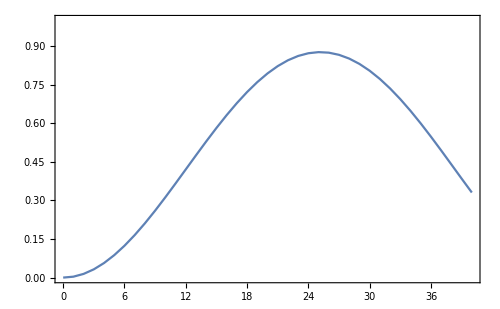

```mathematica
tToτ[t_]=SolveValues[pulseEnd[pulse0]==t,τ][[1]];
tab=ParallelTable[pop[pulse0,tToτ[t]],{t,tMin,tMax,tRes}];
l2=ListPlot[tab,Joined->True,PlotRange->{0,1},DataRange->{tMin 10^3,tMax 10^3}]
```

### Phase scan

```mathematica
(*Δs=Table[2π RandomVariate[NormalDistribution[0 10^3,10^3 ]],{i,1,8}];
tab=ParallelTable[f[ϕ,Δs[[i]]],{i,1,Length[Δs]},{ϕ,0,2π,π/16}];
ListPlot[tab,Joined->True]*)
```

```mathematica
sequence=pPhaseRamsey;
scansPerPoint=20;
tWait=1 10^-3;
tPi=3 10^-6;
Δstd=.1 10^3;
τSeq=SolveValues[Total[Select[sequence,#[[1]]=="w"&][[All,2]]]==tWait,τ][[1]];
f[ϕ1_,Δ1_]=pop[sequence]/.{Ω->π/tPi,η->1,Δ->Δ1,ϕ->ϕ1,τ->τSeq};
```

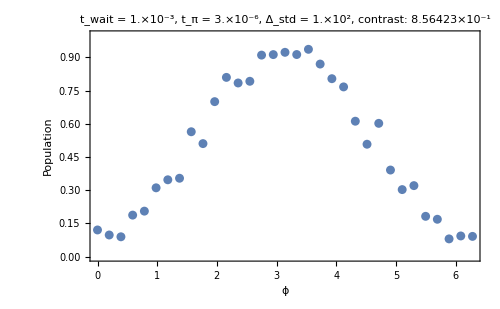

```mathematica
tab=ParallelTable[Mean[Table[f[ϕ,2π RandomVariate[NormalDistribution[0 10^3,Δstd ]]],{i,1,scansPerPoint}]],{ϕ,0,2π,π/16}];
ListPlot[tab,DataRange->{0,2π},PlotRange->{0,1},DataRange->{0,tWait},FrameLabel->{"ϕ","Population"},PlotLabel->StringForm["t_wait = ``, t_π = ``, \nΔ_std = ``, contrast: ``",tWait//N//ScientificForm, tPi//N//ScientificForm,Δstd//N//ScientificForm,ScientificForm[Max[tab]-Min[tab]]]]
```

```mathematica
scansPerPoint=600;
tPi=3 10^-6;
Δstd=500;
contrastF[tWait_]:=Module[{},sequence=pPhaseRamsey;
f[ϕ1_,Δ1_]=pop[sequence]//.{τ->(τ/.Solve[Total[Select[sequence,#[[1]]=="w"&][[All,2]]]==tWait,τ][[1]]),Ω->π/tPi,η->1,Δ->Δ1,ϕ->ϕ1};
tab=Table[Mean[Table[f[ϕ,2π RandomVariate[NormalDistribution[0 10^3,Δstd ]]],{i,1,scansPerPoint}]],{ϕ,0,2π,π/8}];
contrast=Max[tab]-Min[tab]]
```

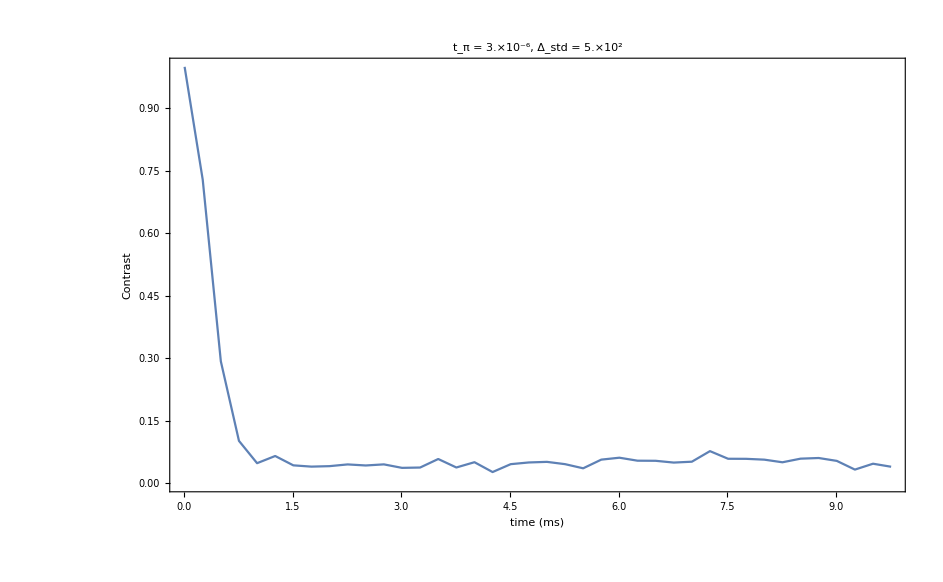

```mathematica
ptab=ParallelTable[{t,contrastF[t 10^-3]},{t,.01,10,.25}];
ListPlot[ptab,PlotRange->{0,1},DataRange->{0,10},FrameLabel->{"time (ms)","Contrast"},PlotLabel->StringForm["t_π = ``, Δ_std = ``", tPi//N//ScientificForm,Δstd//N//ScientificForm],Joined->True]
```